Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
Zmm=(GetYodaRaw[NotebookDirectory[]<>"Zmm.yoda"]);
```

1 Imported ..Histo1D..  /ATLAS_1603_09222/Mee/0

2 Imported ..Histo1D..  /ATLAS_1603_09222/Mmm/0

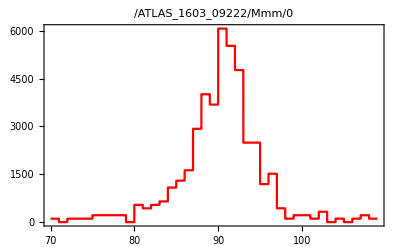

```mathematica
Hmm=HistogramPlot[Zmm[[2]],PlotStyle->{Red}]
```

```mathematica
Zee=(GetYodaRaw[NotebookDirectory[]<>"Zee.yoda"]);
```

1 Imported ..Histo1D..  /ATLAS_1603_09222/Mee/0

2 Imported ..Histo1D..  /ATLAS_1603_09222/Mmm/0

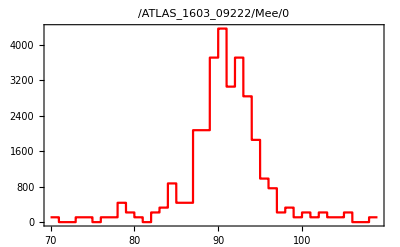

```mathematica
Hee=HistogramPlot[Zee[[1]],PlotStyle->{Red}]
```